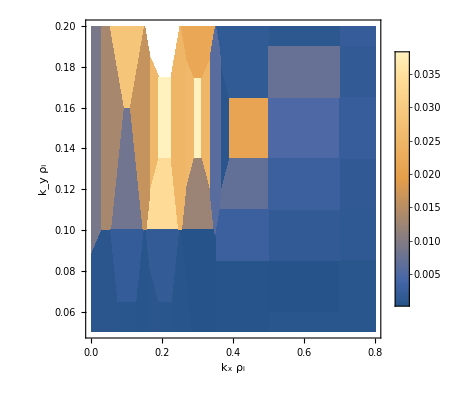

```mathematica
(*Density plot*)
data=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\DIIID\\Plot\\data.xlsx"];

ListDensityPlot[data,Mesh-> None,InterpolationOrder->0,PlotRange->{{0,0.8},{0.05,0.2}},
Axes->True
,
FrameLabel->{Style[ToExpression["k_x \\rho_i",TeXForm,HoldForm
]
,Bold,20],
Style[ToExpression["k_y  \\rho_i",TeXForm,HoldForm
]
,Bold,20]},
LabelStyle->{18,GrayLevel[0]},
PlotLegends->Automatic
]
```